# State Transition Diagrams

I always found the state transition diagrams interesting in the back of New Kind of Science, and wanted to generate them. The basic idea is to take a list of pairs {input value, output value}, convert them to a rule notation: (Rule@@#&)/@List; and run GraphPlot which is new to Mathematica version 6.

I was also curious about S-boxes and tried AES which has the necessary feature of having same sized inputs and outputs (not true with DES or CAST, etc.). The graph doesn't really mean much, as ciphertexts are never run through an S-box more than once without some sort of diffusion step or permutation network. However, non-linear individual components would suggest less linearity overall. The S-box looks quite random with one curiousity: 0x73 and 0x8F (143 and 115) map to each other.

## Cellular Automata

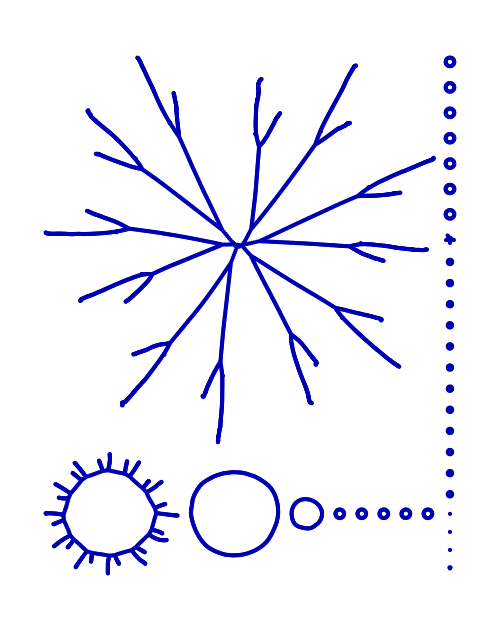

```mathematica
(* Parameters: width, rule, steps *)
(* Warning: Exponential in width, so keep w small *)
w=12;
r=45;
s=1;

(*Code*)
a=Range[2^w-1];
(PadLeft[IntegerDigits[#1,2],w]&)/@a;
b=(FromDigits[Last[CellularAutomaton[r,#1,s]],2]&)/@%;
(Rule@@#1&)/@Transpose[{a,b}];
GraphPlot[%,ImageSize->500]
```

## AES S - box

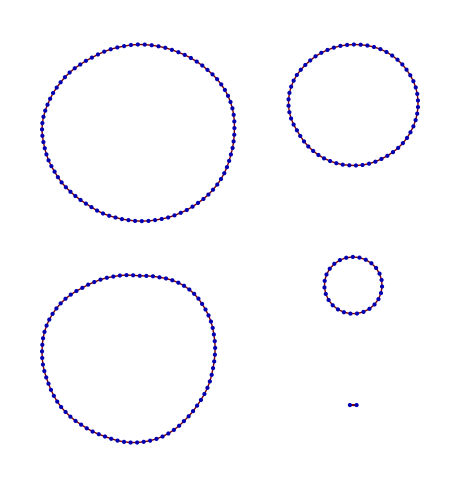

```mathematica
in=Range[0,255];
out={99,124,119,123,242,107,111,197,48,1,103,43,254,215,171,118,202,130,201,125,250,89,71,240,173,212,162,175,156,164,114,192,183,253,147,38,54,63,247,204,52,165,229,241,113,216,49,21,4,199,35,195,24,150,5,154,7,18,128,226,235,39,178,117,9,131,44,26,27,110,90,160,82,59,214,179,41,227,47,132,83,209,0,237,32,252,177,91,106,203,190,57,74,76,88,207,208,239,170,251,67,77,51,133,69,249,2,127,80,60,159,168,81,163,64,143,146,157,56,245,188,182,218,33,16,255,243,210,205,12,19,236,95,151,68,23,196,167,126,61,100,93,25,115,96,129,79,220,34,42,144,136,70,238,184,20,222,94,11,219,224,50,58,10,73,6,36,92,194,211,172,98,145,149,228,121,231,200,55,109,141,213,78,169,108,86,244,234,101,122,174,8,186,120,37,46,28,166,180,198,232,221,116,31,75,189,139,138,112,62,181,102,72,3,246,14,97,53,87,185,134,193,29,158,225,248,152,17,105,217,142,148,155,30,135,233,206,85,40,223,140,161,137,13,191,230,66,104,65,153,45,15,176,84,187,22};

graph=(Rule@@#1&)/@Transpose[{in,out}];
GraphPlot[%,DirectedEdges->False,ImageSize->460]
```

## Random S - boxes

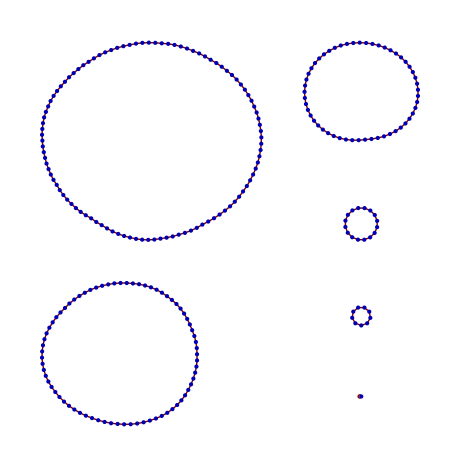

```mathematica
Needs["Combinatorica`"]

n=2^8;
sbox=RandomPermutation[Range[n]];
sub[x_]:=Rule@@{x,sbox[[x]]}
GraphPlot[sub/@Range[n],DirectedEdges->False,ImageSize->460]
```